```mathematica
NotebookDirectory[]
```

/Users/henry/Documents/UW/SPRING_2023/AMATH_583/HW2/

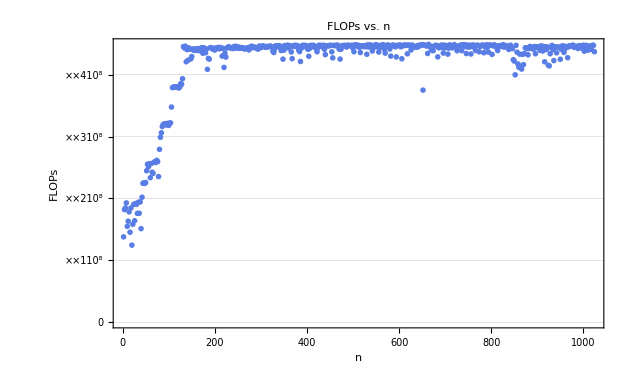

```mathematica
(*Import the data from the output file*)
data=Import["/Users/henry/Documents/UW/SPRING_2023/AMATH_583/HW2/output.txt","CSV"];
(*Create the scatter plot*)
ListPlot[data,PlotTheme->"Business",FrameLabel->{"n","FLOPs"},PlotLabel->"FLOPs vs. n",Frame->True,PlotMarkers->{"OpenMarkers",3},PlotRange->All]
```

```mathematica
?PlotTheme
```

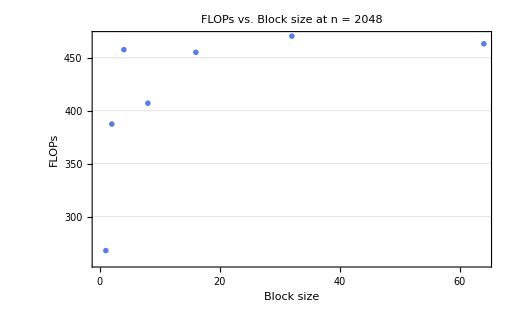

```mathematica
(*Import the data from the output file*)
data=Import["/Users/henry/Documents/UW/SPRING_2023/AMATH_583/HW2/output2.txt","CSV"];
(*Create the scatter plot*)
ListPlot[data,PlotTheme->"Business",FrameLabel->{"Block size","FLOPs"},PlotLabel->"FLOPs vs. Block size at n = 2048",Frame->True,PlotMarkers->{"OpenMarkers",8},PlotRange->All]
```

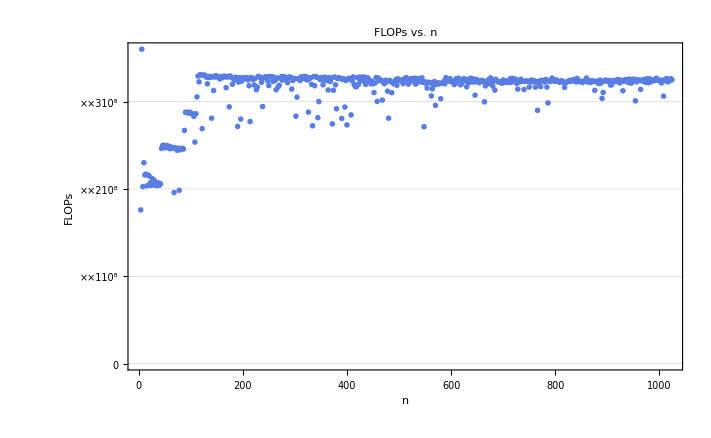

```mathematica
(*Import the data from the output file*)
data=Import["/Users/henry/Documents/UW/SPRING_2023/AMATH_583/HW2/output3.txt","CSV"];
(*Create the scatter plot*)
ListPlot[data,PlotTheme->"Business",FrameLabel->{"n","FLOPs"},PlotLabel->"FLOPs vs. n",Frame->True,PlotMarkers->{"OpenMarkers",3},PlotRange->All]
```